```mathematica
crearegola[n_Integer]:=If[n<3^12,With[{regola=IntegerDigits[n,3,12]},{(#-Mod[#,4])/4,IntegerDigits[Mod[#,4],2,2]}->{regola[[#+1]]}& /@Range[0,11]],Print["Rules number should be from 0 to 531441-1"]]
```

```mathematica
crea[stato_]:= {stato,#}& /@ {{0,0},{0,1},{1,0},{1,1}}
```

```mathematica
$rule98653= crearegola[98653]
```

{{0,{0,0}}→{0},{0,{0,1}}→{1},{0,{1,0}}→{2},{0,{1,1}}→{0},{1,{0,0}}→{0},{1,{0,1}}→{0},{1,{1,0}}→{0},{1,{1,1}}→{2},{2,{0,0}}→{2},{2,{0,1}}→{2},{2,{1,0}}→{1},{2,{1,1}}→{1}}

```mathematica
transform[stati_]:= Flatten[crea[#]/. $rule98653 &  /@ stati]
```

```mathematica
matrice[stati_]:= Module[{p={},d={},s=Partition[stati,2]},Table[If[EvenQ[i],AppendTo[p,s[[i]]],AppendTo[d,s[[i]]]],{i,Length[s]}];With[{L=Sqrt[Length[stati]]},Riffle[Partition[Flatten[d],L],Partition[Flatten[p],L]]]]
```

```mathematica
ArrayPlot[matrice[Nest[transform,{0},6]],Mesh->True]
```

-Graphics-

```mathematica
$rule48653= crearegola[48653]
```

{{0,{0,0}}→{0},{0,{0,1}}→{0},{0,{1,0}}→{2},{0,{1,1}}→{1},{1,{0,0}}→{1},{1,{0,1}}→{0},{1,{1,0}}→{2},{1,{1,1}}→{0},{2,{0,0}}→{1},{2,{0,1}}→{2},{2,{1,0}}→{2},{2,{1,1}}→{2}}

```mathematica
transform[stati_]:= Flatten[crea[#]/. $rule48653 &  /@ stati]
```

```mathematica
ArrayPlot[matrice[Nest[transform,{0},6]],Mesh->True]
```

-Graphics-

```mathematica
creagrafico[n_,steps_]:= With[{myrule=crearegola[n]},(transform[stati_]:= Flatten[crea[#]/. myrule &  /@ stati];ArrayPlot[matrice[Nest[transform,{0},steps]],Mesh->True])]
```

```mathematica
creagrafico[28743,6]
```

-Graphics-

```mathematica
creamatrice[n_,steps_]:= With[{myrule=crearegola[n]},(transform[stati_]:= Flatten[crea[#]/. myrule &  /@ stati];matrice[Nest[transform,{0},steps]])]
```

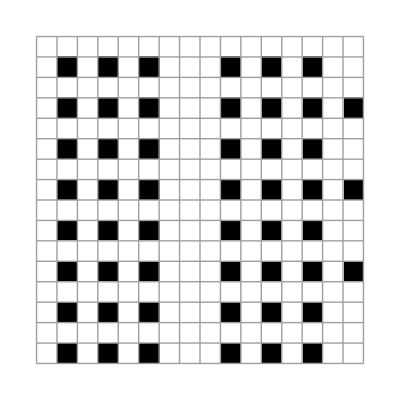

```mathematica
creagrafico[6561,4]
```

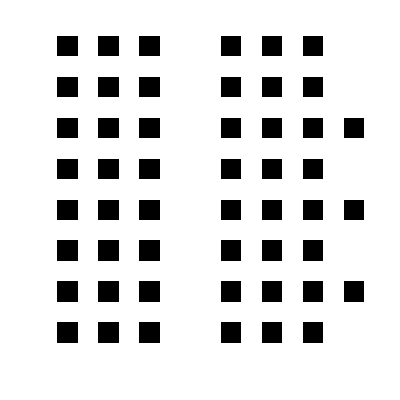

```mathematica
ArrayPlot[Reverse[creamatrice[6561,4],1]]
```

```mathematica
TakeWhile[Range[6561,6722],(creamatrice[#,2]== Transpose[creamatrice[#,2]])&]
```

{6561,6562,6563,6564,6565,6566,6567,6568,6569,6570,6571,6572,6573,6574,6575,6576,6577,6578,6579,6580,6581,6582,6583,6584,6585,6586,6587,6588,6589,6590,6591,6592,6593,6594,6595,6596,6597,6598,6599,6600,6601,6602,6603,6604,6605,6606,6607,6608,6609,6610,6611,6612,6613,6614,6615,6616,6617,6618,6619,6620,6621,6622,6623,6624,6625,6626,6627,6628,6629,6630,6631,6632,6633,6634,6635,6636,6637,6638,6639,6640,6641,6642,6643,6644,6645,6646,6647,6648,6649,6650,6651,6652,6653,6654,6655,6656,6657,6658,6659,6660,6661,6662,6663,6664,6665,6666,6667,6668,6669,6670,6671,6672,6673,6674,6675,6676,6677,6678,6679,6680,6681,6682,6683,6684,6685,6686,6687,6688,6689,6690,6691,6692,6693,6694,6695,6696,6697,6698,6699,6700,6701,6702,6703,6704,6705,6706,6707,6708,6709,6710,6711,6712,6713,6714,6715,6716,6717,6718,6719,6720,6721,6722}

```mathematica
creamatrice[6561,2]== Transpose[creamatrice[6561,2]]
```

True

```mathematica
TakeWhile[Range[6723,7289],(creamatrice[#,2]== Transpose[creamatrice[#,2]])&]
```

{6723,6724,6725,6726,6727,6728,6729,6730,6731,6732,6733,6734,6735,6736,6737,6738,6739,6740,6741,6742,6743,6744,6745,6746,6747,6748,6749,6750,6751,6752,6753,6754,6755,6756,6757,6758,6759,6760,6761,6762,6763,6764,6765,6766,6767,6768,6769,6770,6771,6772,6773,6774,6775,6776,6777,6778,6779,6780,6781,6782,6783,6784,6785,6786,6787,6788,6789,6790,6791,6792,6793,6794,6795,6796,6797,6798,6799,6800,6801,6802,6803}

```mathematica
creamatrice[6773,2]
```

{{0,0,0,0},{0,1,0,1},{0,0,0,0},{0,1,0,2}}

```mathematica
With[{mm=creamatrice[6773,2]},Partition[#,Length[#]/2]& /@  mm]
```

{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}

```mathematica
{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,1]]
```

{{0,0},{0,1},{0,0},{0,1}}

```mathematica
Reverse[%,2]
```

{{0,0},{0,1},{0,0},{0,1}}

```mathematica
Riffle[{{0,0},{1,0},{0,0},{1,0}} ,{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,2]]]
```

{{0,0},{0,0},{1,0},{0,1},{0,0},{0,0},{1,0},{0,2}}

```mathematica
Join[#,#]& /@ {{0,0},{0,0},{1,0},{0,1},{0,0},{0,0},{1,0},{0,2}}
```

```mathematica
Join[Riffle[{{0,0},{1,0},{0,0},{1,0}},{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,2]]]]
```

{{0,0},{0,0},{1,0},{0,1},{0,0},{0,0},{1,0},{0,2}}

```mathematica
Join[#1,#2]& @@ {{{0,0},{1,0},{0,0},{1,0}},{{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,2]]}}
```

{{0,0},{1,0},{0,0},{1,0},{{0,0},{0,1},{0,0},{0,2}}}

```mathematica
Join[{{0,0},{1,0},{0,0},{1,0}},{{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,2]]}]
```

{{0,0},{1,0},{0,0},{1,0},{{0,0},{0,1},{0,0},{0,2}}}

```mathematica
Partition[{{0,0},{0,0},{1,0},{0,1},{0,0},{0,0},{1,0},{0,2}},2]
```

{{{0,0},{0,0}},{{1,0},{0,1}},{{0,0},{0,0}},{{1,0},{0,2}}}

```mathematica
Flatten[{{{0,0},{0,0}},{{1,0},{0,1}},{{0,0},{0,0}},{{1,0},{0,2}}},0]
```

{{{0,0},{0,0}},{{1,0},{0,1}},{{0,0},{0,0}},{{1,0},{0,2}}}

```mathematica
Flatten[#,1]& /@ {{{0,0},{0,0}},{{1,0},{0,1}},{{0,0},{0,0}},{{1,0},{0,2}}}
```

{{0,0,0,0},{1,0,0,1},{0,0,0,0},{1,0,0,2}}

```mathematica
Riffle[Reverse[(Partition[#,Length[#]/2]& )/@  creamatrice[6773,2]][[All,1]],Partition[#,Length[#]/2]& /@  creamatrice[6773,2][[All,2]]]
```

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[0, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[1, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[0, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

{{0,1},Partition[0,0],{0,0},Partition[1,0],{0,1},Partition[0,0],{0,0},Partition[1,0]}

```mathematica
With[{mm=(Partition[#,Length[#]/2]& )/@  creamatrice[6773,2]},Riffle[Reverse[mm[[All,1]],2],mm[[All,2]]]]
```

{{0,0},{0,0},{1,0},{0,1},{0,0},{0,0},{1,0},{0,2}}

```mathematica
(Partition[#,Length[#]/2]& )/@  creamatrice[6773,2]
```

{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}

```mathematica
Riffle[{{0,0},{0,0},{0,1},{0,1},{0,0},{0,0},{0,1},{0,2}}[[All,1]],{{0,0},{0,0},{0,1},{0,1},{0,0},{0,0},{0,1},{0,2}}[[All,2]]]
```

{0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,2}

```mathematica
{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,1]]
```

{{0,0},{0,1},{0,0},{0,1}}

```mathematica
Riffle[Reverse[{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,1]]],{{{0,0},{0,0}},{{0,1},{0,1}},{{0,0},{0,0}},{{0,1},{0,2}}}[[All,2]]]
```

{{0,1},{0,0},{0,0},{0,1},{0,1},{0,0},{0,0},{0,2}}

```mathematica
Join[Riffle[{{a,b},{c,d}},{{1,2},{3,4}}]]
```

{{a,b},{1,2},{c,d},{3,4}}

```mathematica
Join[{a,b},{1,2}]
```

{a,b,1,2}

```mathematica
Join[Riffle[#,#2]&] @@ {{a,1},{b,2}}
```

{a,b,1,2}

```mathematica
With[{mm=(Partition[#,Length[#]/2]& )/@  creamatrice[6773,2]},Partition[Flatten[Riffle[Reverse[mm[[All,1]],2],mm[[All,2]]]],Length[mm]]]
```

{{0,0,0,0},{1,0,0,1},{0,0,0,0},{1,0,0,2}}

```mathematica
Clear[mm]
```

```mathematica
(*qui specchia solo la metà a sinistra della matrice su se stessa*)
```

```mathematica
Ysymm[n_,steps_]:= With[{mm=(Partition[#,Length[#]/2]& )/@  creamatrice[n,steps]},Partition[Flatten[Riffle[Reverse[mm[[All,1]],2],mm[[All,2]]]],Length[mm]]]
```

```mathematica
Ysymm[37623,3]
```

{{0,0,0,0,2,0,1,1},{2,1,2,1,1,2,1,0},{0,0,0,0,2,0,1,1},{2,1,2,1,1,2,1,0},{0,0,1,1,2,0,1,1},{2,1,0,1,1,2,1,0},{0,2,0,2,2,0,0,0},{2,1,2,1,1,2,1,2}}

```mathematica
creamatrice[37623,3]
```

{{0,0,0,0,2,0,1,1},{1,2,1,2,1,2,1,0},{0,0,0,0,2,0,1,1},{1,2,1,2,1,2,1,0},{1,1,0,0,2,0,1,1},{1,0,1,2,1,2,1,0},{2,0,2,0,2,0,0,0},{1,2,1,2,1,2,1,2}}

```mathematica
(*qui specchia la matrice lungo l'asse y, cioè il lato sinistro finisce a destra invertito e viceversa*)
```

```mathematica
With[{mm=(Partition[#,Length[#]/2]& )/@  creamatrice[6773,2]},Partition[Flatten[Riffle[Reverse[mm[[All,2]],2],Reverse[mm[[All,1]],2]]],Length[mm]]]
```

{{0,0,0,0},{1,0,1,0},{0,0,0,0},{2,0,1,0}}

```mathematica
creamatrice[6773,2]
```

{{0,0,0,0},{0,1,0,1},{0,0,0,0},{0,1,0,2}}